## Import EP Packages

Enter the list of required packages (*.m files):

```mathematica
EPPackages={"NumbersPackage.m","LevelStructurePackage.m","HyperfineDipoleCoupling.m", "xmlDataPackage.m", "absorptionImagePackage.m", "MagneticTrapAnalysisPackage.m","MagnetometryPackage.m","AbsorptionImageTypePackage.m","realTimeLoad.m","prototypes.nb"};
```

### Load Packages

In order for loading to work, $EPIncludeDirectory must be set to the local directory containing EP packages.  This can be done automatically at kernel starup by adding the definition in the user initialization file: $BaseDirectory\Kernel\init.m

```mathematica
$BaseDirectory
```

C:\ProgramData\Mathematica

```mathematica
(*Check if $EPIncludeDirectory is properly initialized*)
includeDefined=NameQ["$EPIncludeDirectory"]
```

True

```mathematica
nbFilenameQ[filename_String]:=StringMatchQ[Last[StringSplit[filename,"."]],"nb",IgnoreCase->True];
nbFilenameQ[anything_]:=False;

runInitizationCellsInNotebook[filename_String?nbFilenameQ]:=Module[{nb},
nb=NotebookOpen[$EPIncludeDirectory<>"\\"<>filename];
SetSelectedNotebook[nb];
If[Head[nb]===NotebookObject,
FrontEndExecute[FrontEndToken[nb,"EvaluateInitialization"]];
NotebookClose[nb];
];
];
```

```mathematica
Module[{packageExists,loadPackage,errors},

If[includeDefined,
SetDirectory[$EPIncludeDirectory],

(*$EPIncludeDirectory has not been defined*)
MessageDialog["Error:  $EPIncludeDirectory has not been defined.\n\n"<>"$EPIncludeDirectory must be set to the local directory which contains the EP packages. This can be done automatically at kernel startup by adding the definition in the user initialization file:\n\n"<>$BaseDirectory<>"\\Kernel\\init.m",WindowTitle->"EP Package Error"];Remove[$EPIncludeDirectory];];


packageExists[packageName_]:=If[
Length[Select[FileNames[],#==packageName&]]==1,True,False];

errors="";
loadPackage[package_]:=If[packageExists[package],

If[nbFilenameQ[package],
runInitizationCellsInNotebook[package], (*Directly run initialization cells in *.nb files*)
Get[Evaluate[package]]   (*Get package*)
];,

(*Package not found in $EPIncludeDirectory*)
loadPackage::Error="Missing EP package '"<>package<>"'\n" 
<> "Local EP Package directory is \""<>
If[includeDefined,$EPIncludeDirectory,"NULL"]<>"\\\""
;
Message[loadPackage::Error];
errors=errors<>"* "<>loadPackage::Error<>"\n";];

If[includeDefined,
loadPackage/@EPPackages;
ResetDirectory[];
];

(*Popup dialog box*)
If[StringLength[errors]>0,MessageDialog[errors,WindowTitle->"EP Package Error"];];

];
Remove[includeDefined];
```

Syntax::sntx: Invalid syntax in or before "                                                                                     
                                                                                                                                
                                                                                                                                
             ^" (line 144 of "HyperfineDipoleCoupling.m").

Syntax::sntx: Invalid syntax in or before "\*UnderoverscriptBox[\(\[Sum]\), \(j = 1\),
                                              \(Length[image[\([\)\(1\)\(]\)]]\)]massNorm[\(image[\([\)\(i\)\(]\)]\)[\([\)\(j\)\
                                              (]\)]]\)\);
                                                                                                                                
                                                                                                ^
      " (line 203 of "absorptionImagePackage.m").

## Directories

```mathematica
$HistoryLength=10
```

10

```mathematica
todaysDate=ToString/@Drop[Date[],-3];
dateDir="\\"<>todaysDate⟦1⟧<>"\\"<>todaysDate⟦2⟧<>"\\"<>todaysDate⟦3⟧
```

\2014\1\24

```mathematica
(*dateDir="\\2012\\12\\13";*)
```

```mathematica
pictureDir="\\\\Epsrv1\\ep\\data"<>dateDir<>"\\data\\";
xmlDataDir="\\\\Epsrv1\\ep\\data"<>dateDir<>"\\experiments\\";
xmlSeqDir="\\\\Epsrv1\\ep\\data"<>dateDir<>"\\sequences\\";
```

## Threshold peak finder

### Functions

```mathematica
GetFormatedScopeMeasurement[meas_List,vScale_:1]:=Module[{verticalScale,timeBase},
verticalScale=Cases[meas,{"VerticalScale",_}]⟦1,2⟧//N;
timeBase=Cases[meas,{"TimeBase",_}]⟦1,2⟧//N;
Table[{i*timeBase,#⟦i⟧*vScale},{i,1,Length[#]}]&@Last[meas]
]/;NumberQ[vScale]
```

```mathematica
GetFormatedScopeMeasurement[meas_List,vScale_:1]:=Module[{verticalScale,timeBase},
verticalScale=Cases[meas,{"VerticalScale",_}]⟦1,2⟧//N;
timeBase=Cases[meas,{"TimeBase",_}]⟦1,2⟧//N;
Flatten[Table[{i*timeBase+#⟦1⟧,#⟦2,i⟧*vScale},{i,1,Length[#⟦2⟧]}]&/@Last[meas],1]
]/;NumberQ[vScale]
```

```mathematica
gatherDataByThresholdCut[formatedData_List]:=Module[{deltaXs,dx,breaks},
deltaXs=(#-RotateLeft[#,1])&@formatedData⟦All,1⟧;
dx=Abs[Commonest[deltaXs]⟦1⟧];
breaks=#⟦1⟧&/@({{0}}~Join~Position[(If[Abs[#]>2*dx,1,0]&)/@deltaXs,1]);
Table[Take[formatedData,{1+breaks⟦i⟧,breaks⟦i+1⟧}],{i,1,Length[breaks]-1}]
]
```

```mathematica
getPeakInfoInSection[data_List]:=Module[{peakLoc,sectionRange},
peakLoc=Position[#,Max[#]]⟦1,1⟧&@data;
sectionRange={Min[#],Max[#]}&@data⟦All,1⟧;
{data⟦peakLoc⟧,sectionRange}
]
```

```mathematica
getBiggestPeakFromPeakInfo[allPeaks_List]:=First[Sort[allPeaks,#1⟦1,2⟧>#2⟦1,2⟧&]]⟦1⟧
```

```mathematica
findClosestPeakToTargetFromPeakInfo[allPeaks_List,targetXLocation_]:=Module[{},
First[Sort[{#⟦1⟧,Min[Abs[#⟦2⟧-targetXLocation]]}&/@allPeaks,#1⟦2⟧<#2⟦2⟧&]]⟦1⟧
]
```

```mathematica
findCalibrationUsingAllPeaks[allPeaks_List,fsrXdistance_]:=Module[{biggestPeak,bigPeakXVal,candidatePeaks,allPairs},
biggestPeak=getBiggestPeakFromPeakInfo[allPeaks];
bigPeakXVal=biggestPeak⟦1⟧;
candidatePeaks={biggestPeak};
AppendTo[candidatePeaks,
findClosestPeakToTargetFromPeakInfo[(Drop[#,Position[#,{biggestPeak,_}]⟦1⟧]&@allPeaks),bigPeakXVal-fsrXdistance]];
AppendTo[candidatePeaks,
findClosestPeakToTargetFromPeakInfo[(Drop[#,Position[#,{biggestPeak,_}]⟦1⟧]&@allPeaks),bigPeakXVal+fsrXdistance]];

allPairs={{#1,#2},{#3,#2},{#1,#3}}&@@Sort[candidatePeaks,#1⟦1⟧<#2⟦1⟧&];
Print[candidatePeaks];
(*Pick the pair that has the separation most similar to fsrXdistance.*)
First[Sort[{Abs[Abs[#⟦1,1⟧-#⟦2,1⟧]-fsrXdistance],#}&/@allPairs]]⟦2⟧

(*Take[Sort[candidatePeaks,#1⟦1⟧<#2⟦1⟧&],Min[2,Length[candidatePeaks]]]*)
]
```

```mathematica
findCalibration[formatedCalibrationData_List,fsrXdistance_]:=findCalibrationUsingAllPeaks[(getPeakInfoInSection/@gatherDataByThresholdCut[formatedCalibrationData]),fsrXdistance]
```

```mathematica
findCarrierPeakUsingAllPeaks[allPeaks_List,calibrationPeaks_List]:=Module[{calXPos},
calXPos=calibrationPeaks⟦1,1⟧;
findClosestPeakToTargetFromPeakInfo[allPeaks,calXPos]
]
```

```mathematica
findSidebandPeaksUsingAllPeaks[allPeaks_List,calibrationPeaks_List,sidebandSpacing_]:=Module[{calXPos,sideband1,sideband2},
calXPos=calibrationPeaks⟦1,1⟧;
sideband1=findClosestPeakToTargetFromPeakInfo[allPeaks,calibrationPeaks⟦1,1⟧+sidebandSpacing];
sideband2=findClosestPeakToTargetFromPeakInfo[allPeaks,calibrationPeaks⟦2,1⟧-sidebandSpacing];

{sideband1,sideband2}
]
```

```mathematica
findCarrierAndSidebands[formatedSidebandData_List,calibrationPeaks_List,sidebandSpacing_]:=Module[{allPeaks,carrier,sidebands},
allPeaks=(getPeakInfoInSection/@gatherDataByThresholdCut[formatedSidebandData]);
carrier=findCarrierPeakUsingAllPeaks[allPeaks,calibrationPeaks];
sidebands=findSidebandPeaksUsingAllPeaks[allPeaks,calibrationPeaks,sidebandSpacing];
{carrier}~Join~sidebands
]
```

```mathematica
getFeedbackSignals[peaks_List]:=Module[{carrier,sidebands,sidebandDifference,modulationDepth},
carrier=peaks⟦1⟧;
sidebands=Drop[peaks,1];
sidebandDifference=(sidebands⟦1,2⟧-sidebands⟦2,2⟧)/Mean[sidebands⟦All,2⟧];
(*Constructing a quantity that is linear in β up to 5th order corrections*)
(*modulationDepth=√(Mean[sidebands⟦All,2⟧]/(carrier⟦2⟧+Mean[sidebands⟦All,2⟧]));*)
modulationDepth=Mean[sidebands⟦All,2⟧]/carrier⟦2⟧;
{sidebandDifference,modulationDepth}
]
```

### Test

```mathematica
calibrationData2=GetDeviceMeasurements[GetXMLFileName[727,xmlDataDir],{"epscope2","epmezzanine1.stanford.edu","0"}];
```

```mathematica
cal
```

{{0.0131482,4.06},{0.0277718,4.06}}

{{0.0123686,4.06},{0.0272928,4.06}}

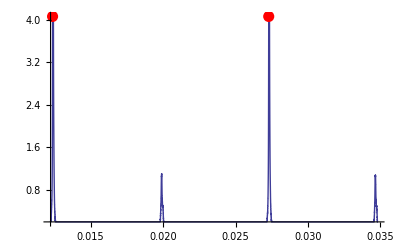

```mathematica
formatedScopeCalData2=GetFormatedScopeMeasurement[calibrationData2⟦1,3⟧];
cal=findCalibration[formatedScopeCalData2,0.015]
ListPlot[formatedScopeCalData2,Joined->True,PlotRange->All,Epilog->{(({Red,PointSize[0.02]}~Join~(Point/@cal)))}]
```

```mathematica
sidebandData2=GetDeviceMeasurements[GetXMLFileName[728,xmlDataDir],{"epscope2","epmezzanine1.stanford.edu","0"}];
formatedSidebandData2=GetFormatedScopeMeasurement[sidebandData2⟦1,3⟧];
```

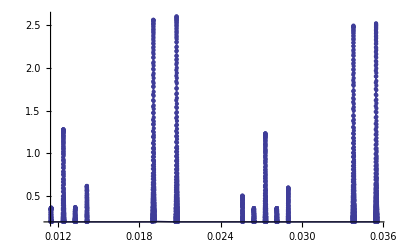

```mathematica
ListPlot[formatedSidebandData2,Joined->True,Mesh->All,PlotRange->All]
```

```mathematica
carrier=findCarrierPeakUsingAllPeaks[(getPeakInfoInSection/@gatherDataByThresholdCut[formatedSidebandData2]),cal]
```

{0.0123782,1.28}

```mathematica
sidebands=findSidebandPeaksUsingAllPeaks[(getPeakInfoInSection/@gatherDataByThresholdCut[formatedSidebandData2]),cal,0.007]
```

{{0.019031,2.56},{0.0207437,2.6}}

```mathematica
findCarrierAndSidebands[formatedSidebandData2,cal,0.007]
```

{{0.0123782,1.28},{0.019031,2.56},{0.0207437,2.6}}

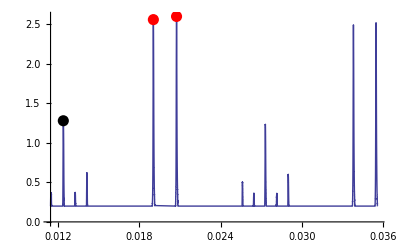

```mathematica
ListPlot[formatedSidebandData2,Joined->True,Epilog->{(({Red,PointSize[0.02]}~Join~(Point/@sidebands))~Join~({Black}~Join~{Point@carrier}))}]
```

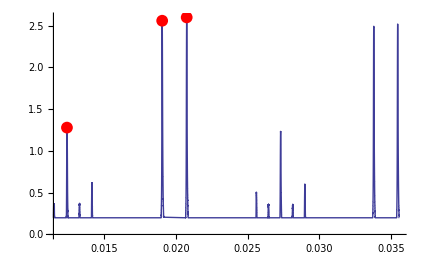

```mathematica
ListPlot[formatedSidebandData2,Joined->True,Epilog->{(({Red,PointSize[0.02]}~Join~(Point/@findCarrierAndSidebands[formatedSidebandData2,cal,0.007])))}]
```

```mathematica
getFeedbackSignals[{{0.01237824,1.28},{0.01903104,2.56},{0.02074368,2.6}}]
```

{-0.0155039,2.01563}

### Compile Work...

```mathematica
Needs["CCodeGenerator`"]
```

```mathematica
functions={findCalibrationCompiled,findCarrierAndSidebandsCompiled,getFeedbackSignalsCompiled}~Join~{commonestCompiled,getPeakInfoInSectionCompiled,gatherByThresholdAndGetPeakInfoInSectionCompiled,getBiggestPeakFromPeakInfoCompiled,findClosestPeakToTargetFromPeakInfoCompiled,findCalibrationUsingAllPeaksCompiled,findCarrierPeakUsingAllPeaksCompiled,findSidebandPeaksUsingAllPeaksCompiled};
functionNames={"findCalibration","findCarrierAndSidebands","getFeedbackSignals"}~Join~{"commonest","getPeakInfoInSection","gatherByThresholdAndGetPeakInfoInSection","getBiggestPeakFromPeakInfo","findClosestPeakToTargetFromPeakInfo","findCalibrationUsingAllPeaks","findCarrierPeakUsingAllPeaks","findSidebandPeaksUsingAllPeaks"};
```

```mathematica
CCodeGenerate[functions,functionNames,dir<>"findPeaks.c"]CCodeGenerate[functions,functionNames,dir<>"findPeaks.h","CodeTarget"->"WolframRTLHeader"]
```

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\findPeaks.c C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\findPeaks.h

```mathematica
CCodeGenerate[commonestCompiled,"commonest",dir<>"commonest.h","CodeTarget"->"WolframRTLHeader"]
CCodeGenerate[commonestCompiled,"commonest",dir<>"commonest.c"]
```

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\commonest.h

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\commonest.c

```mathematica
f=Compile[{x},2x];
f2=Compile[{y},y+f[y],{{f[_],_Real}}];
```

```mathematica
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
```

```mathematica
CCodeGenerate[f,"f",dir<>"f.h","CodeTarget"->"WolframRTLHeader"]
CCodeGenerate[f,"f",dir<>"f.c"]
```

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\f.h

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\f.c

```mathematica
CCodeGenerate[f2,"f2",dir<>"f2.h","CodeTarget"->"WolframRTLHeader"]
CCodeGenerate[f2,"f2",dir<>"f2.c"]
```

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\f2.h

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\f2.c

```mathematica
functions={findCalibrationCompiled,findCarrierAndSidebandsCompiled,getFeedbackSignalsCompiled}~Join~{commonestCompiled,getPeakInfoInSectionCompiled,gatherByThresholdAndGetPeakInfoInSectionCompiled,getBiggestPeakFromPeakInfoCompiled,findClosestPeakToTargetFromPeakInfoCompiled,findCalibrationUsingAllPeaksCompiled,findCarrierPeakUsingAllPeaksCompiled,findSidebandPeaksUsingAllPeaksCompiled};
functionNames={"findCalibration","findCarrierAndSidebands","getFeedbackSignals"}~Join~{"commonest","getPeakInfoInSection","gatherByThresholdAndGetPeakInfoInSection","getBiggestPeakFromPeakInfo","findClosestPeakToTargetFromPeakInfo","findCalibrationUsingAllPeaks","findCarrierPeakUsingAllPeaks","findSidebandPeaksUsingAllPeaks"};
```

```mathematica
functions2={commonestCompiled,getPeakInfoInSectionCompiled,gatherByThresholdAndGetPeakInfoInSectionCompiled,getBiggestPeakFromPeakInfoCompiled,findClosestPeakToTargetFromPeakInfoCompiled,findCalibrationUsingAllPeaksCompiled,findCarrierPeakUsingAllPeaksCompiled,findSidebandPeaksUsingAllPeaksCompiled,findCalibrationCompiled,findCarrierAndSidebandsCompiled,getFeedbackSignalsCompiled};
functionNames2={"commonest","getPeakInfoInSection","gatherByThresholdAndGetPeakInfoInSection","getBiggestPeakFromPeakInfo","findClosestPeakToTargetFromPeakInfo","findCalibrationUsingAllPeaks","findCarrierPeakUsingAllPeaks","findSidebandPeaksUsingAllPeaks","findCalibration","findCarrierAndSidebands","getFeedbackSignals"};
```

```mathematica
CCodeGenerate[functions2,functionNames2,dir<>"findPeaks.c"]CCodeGenerate[functions2,functionNames2,dir<>"findPeaks.h","CodeTarget"->"WolframRTLHeader"]
```

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\findPeaks.c C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\findPeaks.h

```mathematica
includeNum=3;
functions2={commonestCompiled,getPeakInfoInSectionCompiled,gatherByThresholdAndGetPeakInfoInSectionCompiled,getBiggestPeakFromPeakInfoCompiled,findClosestPeakToTargetFromPeakInfoCompiled,findCalibrationUsingAllPeaksCompiled,findCarrierPeakUsingAllPeaksCompiled,findSidebandPeaksUsingAllPeaksCompiled,findCalibrationCompiled,findCarrierAndSidebandsCompiled,getFeedbackSignalsCompiled}//Take[#,includeNum]&;
functionNames2={"commonest","getPeakInfoInSection","gatherByThresholdAndGetPeakInfoInSection","getBiggestPeakFromPeakInfo","findClosestPeakToTargetFromPeakInfo","findCalibrationUsingAllPeaks","findCarrierPeakUsingAllPeaks","findSidebandPeaksUsingAllPeaks","findCalibration","findCarrierAndSidebands","getFeedbackSignals"}//Take[#,includeNum]&;
```

```mathematica
CCodeGenerate[functions2,functionNames2,dir<>"findPeaks.c"]CCodeGenerate[functions2,functionNames2,dir<>"findPeaks.h","CodeTarget"->"WolframRTLHeader"]
```

C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\findPeaks.c C:\Users\Jason\Code\sti\devices\HighPowerSidebandLock\src\mathematica\findPeaks.h

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
CompilePrint[commonestCompiled]
```

1 argument
		10 Integer registers
		3 Real registers
		5 Tensor registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking on
		RuntimeAttributes -> {}

		T(R1)0 = A1
		I3 = 1
		R1 = 1.
		I9 = 2
		I6 = -1
		I7 = 0
		Result = T(R1)3

1	T(R1)1 = Union[ T(R1)0]]
2	I2 = Length[ T(R1)1]
3	I5 = I6
4	T(R2)3 = Table[ I2, I5]
5	I4 = I7
6	goto 14
7	R0 = GetElement[ T(R1)1, I4]
8	T(I2)4 = Position[ T(R1)0, T(R0)0, R1]]
9	I8 = Length[ T(I2)4]
10	R0 = GetElement[ T(R1)1, I4]
11	R2 = I8
12	T(R1)4 ={ R2, R0 }
13	Element[ T(R2)3, I5] = T(R1)4
14	if[ ++ I4 <= I2] goto 7
15	T(R2)1 = Sort[ T(R2)3]]
16	T(R1)3 = Part[ T(R2)1, I6]
17	R0 = Part[ T(R1)3, I9]
18	T(R1)3 ={ R0 }
19	Return

```mathematica
CompilePrint[findPeakWithBiggestValueCompiled]
```

1 argument
		2 Boolean registers
		6 Integer registers
		3 Real registers
		3 Tensor registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking on
		RuntimeAttributes -> {}

		T(R3)0 = A1
		I0 = 1
		R2 = 7.
		I2 = 2
		Result = T(R2)2

1	I1 = I0
2	I3 = I0
3	I4 = Length[ T(R3)0]
4	B0 = I3 <= I4
5	if[ !B0] goto 16
6	R0 = Part[ T(R3)0, I3, I0, I2]
7	R1 = Part[ T(R3)0, I1, I0, I2]
8	B1 = R0 > R1 (tol R2)
9	if[ !B1] goto 12
10	I1 = I3
11	goto 12
12	I4 = I3
13	I5 = I4 + I0
14	I3 = I5
15	goto 3
16	T(R2)2 = Part[ T(R3)0, I1]
17	Return

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[Full]
```

{{Name→Intel Compiler,Compiler→CCompilerDriver`IntelCompiler`IntelCompiler,CompilerInstallation→None,CompilerName→Automatic},{Name→Generic C Compiler,Compiler→CCompilerDriver`GenericCCompiler`GenericCCompiler,CompilerInstallation→None,CompilerName→Automatic}}

```mathematica
DefaultCCompiler[]
```

CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler

```mathematica
$CCompiler
```

Automatic

```mathematica
$CCompiler =
	Automatic
```

Automatic

```mathematica
"Windows-x86-64"
```

```mathematica
$SystemID
```

Remove::rmlck: Symbol $SystemID is Locked and cannot be removed.

```mathematica
$SystemID//Attributes
```

{Locked,Protected}

```mathematica
Unprotect[$SystemID]
```

Protect::locked: Symbol $SystemID is locked.

{}

```mathematica
$SystemID="Windows"
```

Set::wrsym: Symbol $SystemID is Protected.

Windows

### Tests

```mathematica
commonestCompiled[{4,1,1,1,5,1,1,1,1,1,1,6,0,0,0,1,1,1,1,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]
```

{0.}

```mathematica
allPeaks=gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedCalData3]
```

{{{0.0058368,1.14667},{0.00572064,0.005952}},{{0.0131482,4.06},{0.0130032,0.0133334}},{{0.0203914,0.2},{0.0203914,0.0203914}},{{0.0204998,1.14},{0.0203942,0.0206227}},{{0.0277718,4.06},{0.0276355,0.027961}},{{0.0349488,0.293333},{0.0349402,0.0349488}}}

```mathematica
getBiggestPeakFromPeakInfoCompiled[gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedCalData3]]
```

{0.0277718,4.06}

```mathematica
findClosestPeakToTargetFromPeakInfoCompiled[gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedCalData3],0.1]
```

{0.0349488,0.293333}

```mathematica
findCalibrationUsingAllPeaksCompiled[allPeaks,0.015]
```

{{0.0131482,4.06},{0.0277718,4.06}}

```mathematica
gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedCalData3]
```

{{{0.0058368,1.14667},{0.00572064,0.005952}},{{0.0131482,4.06},{0.0130032,0.0133334}},{{0.0203914,0.2},{0.0203914,0.0203914}},{{0.0204998,1.14},{0.0203942,0.0206227}},{{0.0277718,4.06},{0.0276355,0.027961}},{{0.0349488,0.293333},{0.0349402,0.0349488}}}

```mathematica
findCalibrationCompiled[formatedCalData3,0.015]
```

{{0.0131482,4.06},{0.0277718,4.06}}

```mathematica
gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedCalData3]
```

{{{0.0058368,1.14667},{0.00572064,0.005952}},{{0.0131482,4.06},{0.0130032,0.0133334}},{{0.0203914,0.2},{0.0203914,0.0203914}},{{0.0204998,1.14},{0.0203942,0.0206227}},{{0.0277718,4.06},{0.0276355,0.027961}},{{0.0349488,0.293333},{0.0349402,0.0349488}}}

```mathematica
cal=findCalibrationCompiled[formatedCalData3,0.015]
```

{{0.0131482,4.06},{0.0277718,4.06}}

```mathematica
dir="C:\\Users\\Jason\\Desktop\\mathematicaToC\\";
```

```mathematica
Export[dir<>"testPeakFun.c",findCarrierAndSidebandsCompiled]
```

C:\Users\Jason\Desktop\mathematicaToC\testPeakFun.c

```mathematica
peaks=findCarrierAndSidebandsCompiled[formatedSidebandData3,cal,0.0066]
```

{{0.0131779,1.7},{0.0196675,2.52667},{0.0213389,2.48}}

```mathematica
getFeedbackSignalsCompiled@peaks
```

{0.0186418,1.47255}

## Convert to C; added carrier offset

### Compiled Functions

```mathematica
commonest[data_List]:={Last[Sort[{Length[#],#⟦1⟧}&/@Gather[data]]]⟦2⟧}
```

```mathematica
commonestCompiled=Compile[{{data,_Real,1}},
{Last[Sort[{Length[Position[data,#]],#}&/@Union[data]]]⟦2⟧}
];
```

```mathematica
getPeakInfoInSectionCompiled=Compile[{{data,_Real,2}},
Module[{peakLoc,sectionRange},
peakLoc=Position[#,Max[#]]⟦1,1⟧&@data;
sectionRange={Min[#],Max[#]}&@data⟦All,1⟧;
{data⟦peakLoc⟧,sectionRange}
]
];
```

```mathematica
gatherByThresholdAndGetPeakInfoInSectionCompiled=Compile[{{formatedData,_Real,2}},
(*Combining two functions here, to avoid generating an illegal nontensor object.*)
Module[{deltaXs,dx,breaks},
(*deltaXs=(#-RotateLeft[#,1])&@formatedData⟦All,1⟧;*)
deltaXs=Table[(formatedData⟦i,1⟧-formatedData⟦Mod[i,Length[formatedData]]+1,1⟧),{i,1,Length[formatedData]}];
dx=Abs[commonestCompiled[deltaXs]⟦1⟧];
breaks=#⟦1⟧&/@({{0}}~Join~Position[(If[Abs[#]>2*dx,1,0]&)/@deltaXs,1]);

Table[getPeakInfoInSectionCompiled[Take[formatedData,{1+breaks⟦i⟧,breaks⟦i+1⟧}]],{i,1,Length[breaks]-1}]
],
{{getPeakInfoInSectionCompiled[_],_Real,2},{commonestCompiled[_],_Real,1}},CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
gatherByThresholdAndGetPeakInfoInSectionWithLimitsCompiled=Compile[{{formatedData,_Real,2}},
(*Combining two functions here, to avoid generating an illegal nontensor object.*)
Module[{deltaXs,dx,breaks,max,min},
(*deltaXs=(#-RotateLeft[#,1])&@formatedData⟦All,1⟧;*)
deltaXs=Table[(formatedData⟦i,1⟧-formatedData⟦Mod[i,Length[formatedData]]+1,1⟧),{i,1,Length[formatedData]}];
dx=Abs[commonestCompiled[deltaXs]⟦1⟧];
breaks=#⟦1⟧&/@({{0}}~Join~Position[(If[Abs[#]>2*dx,1,0]&)/@deltaXs,1]);

max=Max[formatedData⟦All,2⟧];
min=Min[formatedData⟦All,2⟧];

Select[Table[getPeakInfoInSectionCompiled[Take[formatedData,{1+breaks⟦i⟧,breaks⟦i+1⟧}]],{i,1,Length[breaks]-1}],(#⟦1,2⟧>min&&#⟦1,2⟧<max)&]
],
{{getPeakInfoInSectionCompiled[_],_Real,2},{commonestCompiled[_],_Real,1}},CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
findPeakWithBiggestValueCompiled//Clear
```

```mathematica
findPeakWithBiggestValueCompiled=Compile[{{allPeaks,_Real,3},{minimumX,_Real}},
Module[{i,biggestPos},
i=1;
(*Pick the starting peak for the search. Make sure it has at least the minimum x value. *)
While[allPeaks⟦i,1,1⟧<minimumX&&i<Length[allPeaks],i++;];
biggestPos=i;
For[i=1,i≤Length[allPeaks],i++,
(*Find the biggest peak, making sure the x value is larger than minimumX. *)
If[allPeaks⟦i,1,2⟧>allPeaks⟦biggestPos,1,2⟧&&allPeaks⟦i,1,1⟧>minimumX,biggestPos=i;];
];
allPeaks⟦biggestPos⟧
],
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
getBiggestPeakFromPeakInfoCompiled=Compile[{{allPeaks,_Real,3},{minimumX,_Real}},
findPeakWithBiggestValueCompiled[allPeaks,minimumX]⟦1⟧
,CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}];
```

```mathematica
findItemWithBiggestValueAtSubindex[data_List,subindices_List]:=Module[{i,biggest},
If[Length[data]>0,biggest=data⟦1⟧;,biggest=0;];
For[i=1,i≤Length[data],i++,
If[Extract[data⟦i⟧,subindices]>Extract[biggest,subindices],biggest=data⟦i⟧;];
];
biggest
]
```

```mathematica
findClosestPeakToTargetFromPeakInfoCompiled//Clear
```

```mathematica
findClosestPeakToTargetFromPeakInfoCompiled=Compile[{{allPeaks,_Real,3},{targetXLocation,_Real},{targetRange,_Real},{minimumX,_Real}},
Module[{i,smallestLoc,bestPeakHeight,searchRange},

smallestLoc=-1;
bestPeakHeight=0.0;
(*Min[Abs[allPeaks⟦i,2⟧-targetXLocation]]*)
searchRange=0.5*targetRange;
While[(smallestLoc <0)&&(searchRange<100*targetRange),
For[i=1,i≤Length[allPeaks],i++,
If[Abs[allPeaks⟦i,1,1⟧-targetXLocation]<searchRange,
(*Find the biggest peak within the target range, making sure the peak x value is larger than minimumX. *)
If[allPeaks⟦i,1,2⟧>bestPeakHeight&&allPeaks⟦i,1,1⟧>minimumX,
smallestLoc=i;
bestPeakHeight=allPeaks⟦i,1,2⟧;
];

];
];
searchRange+=0.5*targetRange;

];

allPeaks⟦smallestLoc,1⟧

(*{1,1} is a hack to make the intermediate tensor rectangular*)
(*First[Sort[{#⟦1⟧,{1,1}*Min[Abs[#⟦2⟧-targetXLocation]]}&/@allPeaks,#1⟦2,1⟧<#2⟦2,1⟧&]]⟦1⟧*)
]
];
```

```mathematica
findCalibrationUsingAllPeaksCompiled//Clear
```

```mathematica
findCalibrationUsingAllPeaksCompiled=Compile[{{allPeaks,_Real,3},{fsrXdistance,_Real},{minimumX,_Real}},
Module[{biggestPeak,bigPeakXVal,candidatePeaks,d12,d32,d13,bestPeaks,skippedPeak},
biggestPeak=getBiggestPeakFromPeakInfoCompiled[allPeaks,minimumX];
bigPeakXVal=biggestPeak⟦1⟧;
candidatePeaks={biggestPeak};
(*(Drop[allPeaks,Position[allPeaks,{biggestPeak,_}]⟦1⟧])*)
AppendTo[candidatePeaks,
findClosestPeakToTargetFromPeakInfoCompiled[allPeaks,bigPeakXVal-fsrXdistance,0.1*fsrXdistance,minimumX]];AppendTo[candidatePeaks,
findClosestPeakToTargetFromPeakInfoCompiled[allPeaks,bigPeakXVal+fsrXdistance,0.1*fsrXdistance,minimumX]];

(*allPairs={{#1,#2},{#3,#2},{#1,#3}}&@@Sort[candidatePeaks,#1⟦1⟧<#2⟦1⟧&];*)
(*allPairs={{#⟦1⟧,#⟦2⟧},{#⟦3⟧,#⟦2⟧},{#⟦1⟧,#⟦3⟧}}&@Sort[candidatePeaks,#1⟦1⟧<#2⟦1⟧&];*)

(*Pick the pair that has the separation most similar to fsrXdistance.*)
d12=Abs[Abs[candidatePeaks⟦1⟧⟦1⟧-candidatePeaks⟦2⟧⟦1⟧]-fsrXdistance];
d32=Abs[Abs[candidatePeaks⟦3⟧⟦1⟧-candidatePeaks⟦2⟧⟦1⟧]-fsrXdistance];
d13=Abs[Abs[candidatePeaks⟦1⟧⟦1⟧-candidatePeaks⟦3⟧⟦1⟧]-fsrXdistance];


(*{{1,1},{1,1}} is a hack to make the intermediate tensor rectangular*)
(*First[Sort[{Abs[Abs[#⟦1,1⟧-#⟦2,1⟧]-fsrXdistance]*{{1,1},{1,1}},#}&/@allPairs,#1⟦1,1,1⟧<#2⟦1,1,1⟧&]]⟦2⟧*)

bestPeaks=
If[d12<d32,
If[d12<d13,{1,2},
If[d13<d32,{1,3},{3,2}]
],
If[d32<d13,{3,2},
If[d13<d12,{1,3},{1,2}]
]
];

skippedPeak=Complement[{1,2,3},bestPeaks]⟦1⟧;

If[Abs[candidatePeaks⟦bestPeaks⟦1⟧,1⟧-candidatePeaks⟦skippedPeak,1⟧]/fsrXdistance<0.1&&candidatePeaks⟦bestPeaks⟦1⟧,2⟧<candidatePeaks⟦skippedPeak,2⟧,bestPeaks={skippedPeak,bestPeaks⟦2⟧};];
If[Abs[candidatePeaks⟦bestPeaks⟦2⟧,1⟧-candidatePeaks⟦skippedPeak,1⟧]/fsrXdistance<0.1&&candidatePeaks⟦bestPeaks⟦2⟧,2⟧<candidatePeaks⟦skippedPeak,2⟧,bestPeaks={bestPeaks⟦1⟧,skippedPeak};];

(*Arrange in accending X order*)
If[candidatePeaks⟦bestPeaks⟦1⟧,1⟧<candidatePeaks⟦bestPeaks⟦2⟧,1⟧,{candidatePeaks⟦bestPeaks⟦1⟧⟧,candidatePeaks⟦bestPeaks⟦2⟧⟧},{candidatePeaks⟦bestPeaks⟦2⟧⟧,candidatePeaks⟦bestPeaks⟦1⟧⟧}]


],
{{getBiggestPeakFromPeakInfoCompiled[_,_],_Real,1},{findClosestPeakToTargetFromPeakInfoCompiled[_,_,_,_],_Real,1}},CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
findCalibrationCompiled=Compile[{{formatedCalibrationData,_Real,2},{fsrXdistance,_Real},{minimumX,_Real}},
Module[{allPeaks},
allPeaks=gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedCalibrationData];
findCalibrationUsingAllPeaksCompiled[allPeaks,fsrXdistance,minimumX]
],
{{gatherByThresholdAndGetPeakInfoInSectionCompiled[_],_Real,3},{findCalibrationUsingAllPeaksCompiled[_,_],_Real,2}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
Clear[findCarrierPeakUsingAllPeaksCompiled]
```

```mathematica
findCarrierPeakUsingAllPeaksCompiled=Compile[{{allPeaks,_Real,3},{calibrationPeaks,_Real,2},{targetRange,_Real},{minimumX,_Real},{carrierOffset,_Real}},
Module[{carrierL,carrierR},
carrierL=findClosestPeakToTargetFromPeakInfoCompiled[allPeaks,calibrationPeaks⟦1,1⟧+carrierOffset,targetRange,minimumX];
carrierR=findClosestPeakToTargetFromPeakInfoCompiled[allPeaks,calibrationPeaks⟦2,1⟧+carrierOffset,targetRange,minimumX];
{carrierL,carrierR}
],
{{findClosestPeakToTargetFromPeakInfoCompiled[_,_,_,_],_Real,1}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
findCarriersCompiled=Compile[{{formatedSidebandData,_Real,2},{calibrationPeaks,_Real,2},{minimumX,_Real},{targetRange,_Real},{carrierOffset,_Real}},
Module[{allPeaks,bothCarriers},
allPeaks=gatherByThresholdAndGetPeakInfoInSectionWithLimitsCompiled[formatedSidebandData];
bothCarriers=findCarrierPeakUsingAllPeaksCompiled[allPeaks,calibrationPeaks,targetRange,minimumX,carrierOffset];
bothCarriers
],
{{gatherByThresholdAndGetPeakInfoInSectionWithLimitsCompiled[_],_Real,3},{findCarrierPeakUsingAllPeaksCompiled[_,_,_,_,_],_Real,2}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
Clear[findSidebandPeaksUsingAllPeaksCompiled]
```

```mathematica
findSidebandPeaksUsingAllPeaksCompiled=Compile[{{allPeaks,_Real,3},{referencePeaks,_Real,2},{sidebandSpacing,_Real},{targetRange,_Real},{minimumX,_Real},{carrierOffset,_Real}},
Module[{sideband1,sideband2},
sideband1=findClosestPeakToTargetFromPeakInfoCompiled[allPeaks,referencePeaks⟦1,1⟧+sidebandSpacing+carrierOffset,targetRange,minimumX];
sideband2=findClosestPeakToTargetFromPeakInfoCompiled[allPeaks,referencePeaks⟦2,1⟧-sidebandSpacing+carrierOffset,targetRange,minimumX];
If[sideband1⟦1⟧<sideband2⟦1⟧,{sideband1,sideband2},{sideband2,sideband1}]

],
{{findClosestPeakToTargetFromPeakInfoCompiled[_,_,_,_],_Real,1}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
findFirstSidebandsCompiled=Compile[{{formatedSidebandData,_Real,2},{calibrationPeaks,_Real,2},{sidebandSpacing,_Real},{minimumX,_Real},{targetRange,_Real},{carrierOffset,_Real}},
Module[{allPeaks,sidebands},
allPeaks=gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedSidebandData];
sidebands=findSidebandPeaksUsingAllPeaksCompiled[allPeaks,calibrationPeaks,sidebandSpacing,targetRange,minimumX,carrierOffset];
sidebands
],
{{gatherByThresholdAndGetPeakInfoInSectionCompiled[_],_Real,3},{findSidebandPeaksUsingAllPeaksCompiled[_,_,_,_,_,_],_Real,2}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
findCarrierAndSidebandsCompiled=Compile[{{formatedSidebandData,_Real,2},{calibrationPeaks,_Real,2},{sidebandSpacing,_Real},{minimumX,_Real},{targetRange,_Real}},
Module[{allPeaks,bothCarriers,sidebands,fsr},
fsr=Abs[calibrationPeaks⟦1,1⟧-calibrationPeaks⟦2,1⟧];
allPeaks=gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedSidebandData];
bothCarriers=findCarrierPeakUsingAllPeaksCompiled[allPeaks,calibrationPeaks,targetRange,minimumX,0];
(*Use the carriers as reference instead of the calibration, since things might drift.*)
sidebands=findSidebandPeaksUsingAllPeaksCompiled[allPeaks,bothCarriers,sidebandSpacing,targetRange,minimumX,0];
{bothCarriers⟦1⟧}~Join~sidebands
],
{{gatherByThresholdAndGetPeakInfoInSectionCompiled[_],_Real,3},{findCarrierPeakUsingAllPeaksCompiled[_,_,_,_,_],_Real,2},{findSidebandPeaksUsingAllPeaksCompiled[_,_,_,_,_],_Real,2}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
getFeedbackSignalsCompiled=Compile[{{peaks,_Real,2}},
Module[{carrier,sidebands,sidebandDifference,modulationDepth},
carrier=peaks⟦1⟧;
sidebands=Drop[peaks,1];
sidebandDifference=(sidebands⟦1,2⟧-sidebands⟦2,2⟧)/Mean[sidebands⟦All,2⟧];
(*Constructing a quantity that is linear in β up to 5th order corrections*)
(*modulationDepth=√(Mean[sidebands⟦All,2⟧]/(carrier⟦2⟧+Mean[sidebands⟦All,2⟧]));*)
modulationDepth=Mean[sidebands⟦All,2⟧]/carrier⟦2⟧;
{sidebandDifference,modulationDepth}
]
];
```

```mathematica
getFeedbackSignalsHighLowCompiled=Compile[{{sidebandPeaks,_Real,2},{carrierPeaks,_Real,2}},
Module[{carrier,sidebands,sidebandDifference,modulationDepth},
carrier=carrierPeaks⟦1⟧;
sidebands=sidebandPeaks;
sidebandDifference=(sidebands⟦1,2⟧-sidebands⟦2,2⟧)/Mean[sidebands⟦All,2⟧];
(*Constructing a quantity that is linear in β up to 5th order corrections*)
(*modulationDepth=√(Mean[sidebands⟦All,2⟧]/(carrier⟦2⟧+Mean[sidebands⟦All,2⟧]));*)
modulationDepth=Mean[sidebands⟦All,2⟧]/carrier⟦2⟧;
{sidebandDifference,modulationDepth}
]
];
```

```mathematica
(*findFirstAndSecondOrderSidebandsCompiled=Compile[{{formatedSidebandData,_Real,2},{calibrationPeaks,_Real,2},{firstOrderSidebandSpacing,_Real},{secondOrderSidebandSpacing,_Real},{minimumX,_Real},{targetRange,_Real}},
Module[{allPeaks,firstOrderSidebands,secondOrderSidebands,fsr},
fsr=Abs[calibrationPeaks⟦1,1⟧-calibrationPeaks⟦2,1⟧];
allPeaks=gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedSidebandData];

(*Use the carriers as reference instead of the calibration, since things might drift.*)
firstOrderSidebands=findSidebandPeaksUsingAllPeaksCompiled[allPeaks,calibrationPeaks,firstOrderSidebandSpacing,targetRange,minimumX];
secondOrderSidebands=findSidebandPeaksUsingAllPeaksCompiled[allPeaks,calibrationPeaks,secondOrderSidebandSpacing,targetRange,minimumX];
firstOrderSidebands~Join~secondOrderSidebands
],
{{gatherByThresholdAndGetPeakInfoInSectionCompiled[_],_Real,3},{findCarrierPeakUsingAllPeaksCompiled[_,_,_,_],_Real,2},{findSidebandPeaksUsingAllPeaksCompiled[_,_,_,_,_],_Real,2}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];*)
```

```mathematica
findFirstAndSecondOrderSidebandsCompiled=Compile[{{formatedSidebandData,_Real,2},{calibrationPeaks,_Real,2},{firstOrderSidebandSpacing,_Real},{secondOrderSidebandSpacing,_Real},{minimumX,_Real},{targetRange,_Real},{carrierOffset,_Real}},
Module[{allPeaks,firstOrderSidebands,secondOrderSidebands,fsr,calibrationPeaksOffset},
fsr=Abs[calibrationPeaks⟦1,1⟧-calibrationPeaks⟦2,1⟧];
allPeaks=gatherByThresholdAndGetPeakInfoInSectionCompiled[formatedSidebandData];
calibrationPeaksOffset={{calibrationPeaks⟦1,1⟧+carrierOffset,calibrationPeaks⟦1,2⟧},{calibrationPeaks⟦2,1⟧+carrierOffset,calibrationPeaks⟦2,2⟧}};
(*Use the carriers as reference instead of the calibration, since things might drift.*)
firstOrderSidebands=findSidebandPeaksUsingAllPeaksCompiled[allPeaks,calibrationPeaksOffset,firstOrderSidebandSpacing,targetRange,minimumX];
secondOrderSidebands=findSidebandPeaksUsingAllPeaksCompiled[allPeaks,calibrationPeaksOffset,secondOrderSidebandSpacing,targetRange,minimumX];
firstOrderSidebands~Join~secondOrderSidebands
],
{{gatherByThresholdAndGetPeakInfoInSectionCompiled[_],_Real,3},{findCarrierPeakUsingAllPeaksCompiled[_,_,_,_],_Real,2},{findSidebandPeaksUsingAllPeaksCompiled[_,_,_,_,_],_Real,2}},
CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

```mathematica
getFeedbackSignalsFromFirstAndSecondSidebandsCompiled=Compile[{{peaks,_Real,2}},
Module[{firstOrderSidebands,secondOrderSidebands,sidebandDifference,modulationDepth},
firstOrderSidebands=Take[peaks,2];
secondOrderSidebands=Drop[peaks,2];
sidebandDifference=(firstOrderSidebands⟦1,2⟧-firstOrderSidebands⟦2,2⟧)/Mean[firstOrderSidebands⟦All,2⟧];

modulationDepth=Mean[secondOrderSidebands⟦All,2⟧]/Mean[firstOrderSidebands⟦All,2⟧];
{sidebandDifference,modulationDepth}
]
];
```

### Export to C

```mathematica
dir="C:\\Users\\Jason\\Code\\sti\\devices\\HighFreqSidebandLock\\src\\mathematica\\";
```

```mathematica
Export[dir<>"findCalibration.c",findCalibrationCompiled];
```

```mathematica
Export[dir<>"findCarrierAndSidebands.c",findCarrierAndSidebandsCompiled];
```

```mathematica
Export[dir<>"getFeedbackSignals.c",getFeedbackSignalsCompiled];
```

```mathematica
Export[dir<>"findFirstAndSecondOrderSidebands.c",findFirstAndSecondOrderSidebandsCompiled];
```

```mathematica
Export[dir<>"getFeedbackSignalsFromFirstAndSecondSidebands.c",getFeedbackSignalsFromFirstAndSecondSidebandsCompiled];
```

High frequency lock versions:

```mathematica
Export[dir<>"findFirstSidebands.c",findFirstSidebandsCompiled];
```

```mathematica
Export[dir<>"findCarriers.c",findCarriersCompiled];
```

```mathematica
Export[dir<>"getFeedbackSignalsHighLow.c",getFeedbackSignalsHighLowCompiled];
```